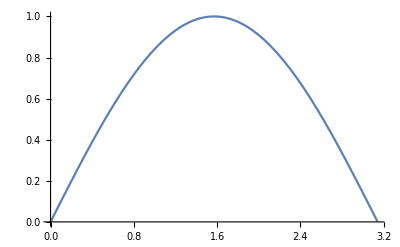

```mathematica
Plot[Sin[x],{x,0,3.14}]
```

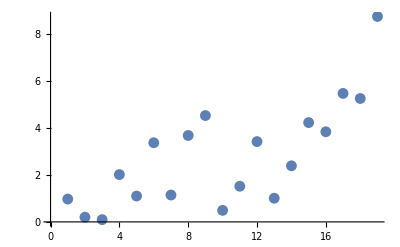

```mathematica
ListPlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

```mathematica
ListLinePlot[Table[RandomReal[x],{x,1,10,0.5}]]
```

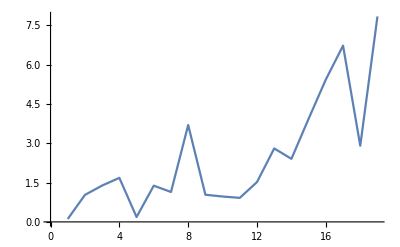

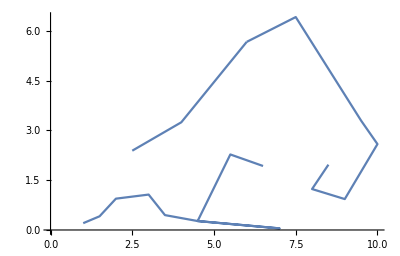

```mathematica
ListCurvePathPlot[Table[{x,RandomReal[x]},{x,1,10,0.5}]]
```

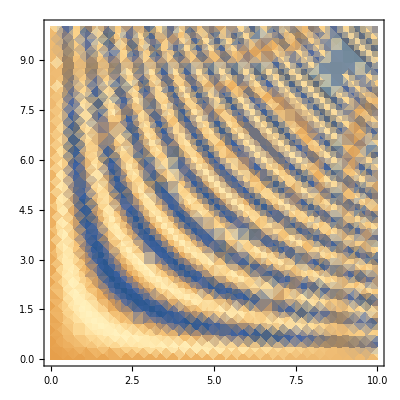

```mathematica
DensityPlot[Sin[x*y],{x,0,10},{y,0,10}]
```

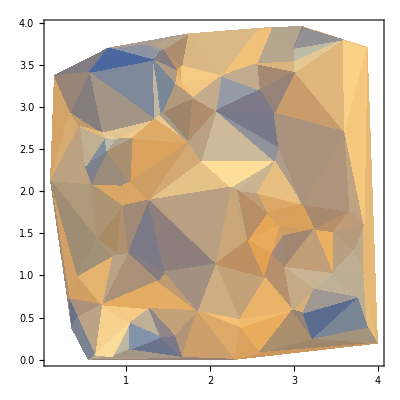

```mathematica
ListDensityPlot[RandomReal[{0,4},{100,3}]]
```

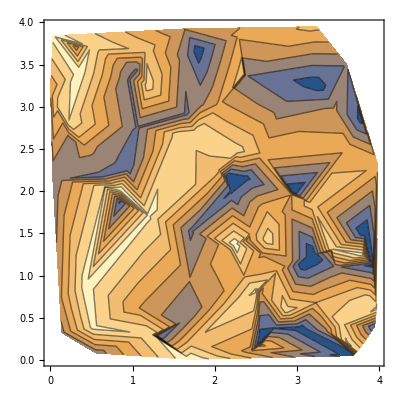

```mathematica
ListContourPlot[RandomReal[{0,4},{100,3}]]
```

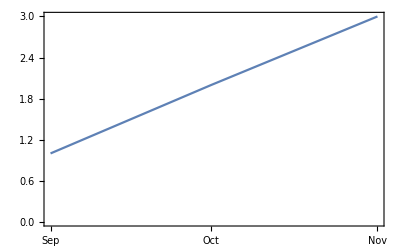

```mathematica
DateListPlot[{1,2,3},{2008,9}]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/3},{t,0,15}]
```

-Graphics3D-

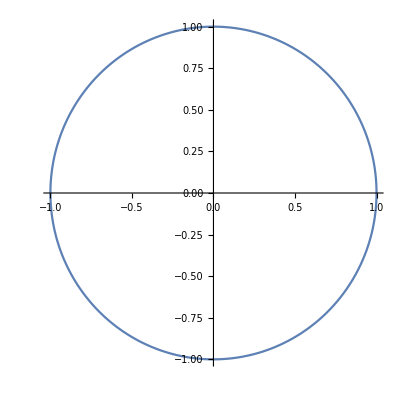

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

```mathematica
Needs["StatisticalPlots`"]
```

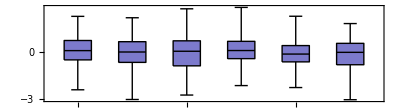

```mathematica
BoxWhiskerPlot[RandomReal[NormalDistribution[0,1],{100,6}]]
```

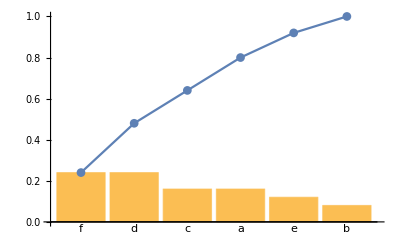

```mathematica
data=RandomChoice[CharacterRange["a","f"],{25}];
ParetoPlot[data]
```

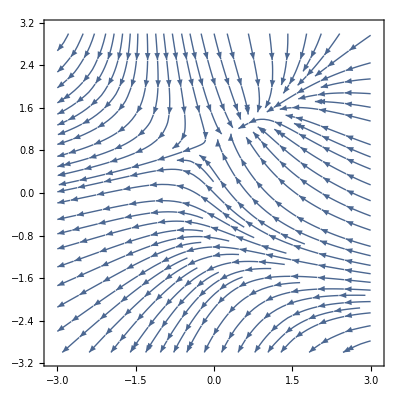

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
StreamPlot[{{x,y},{y,-x}},{x,-3,3},{y,-3,3}]
```

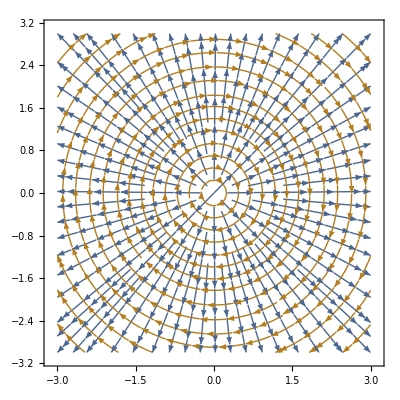

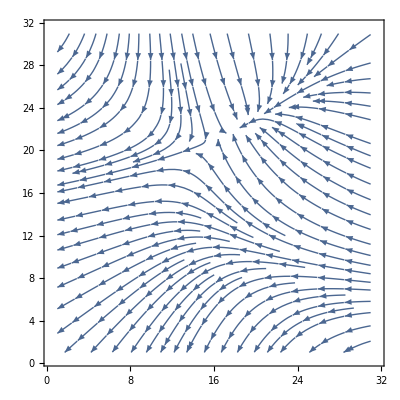

```mathematica
data=Table[{-1-x^2+y,1+x-y^2},{x,-3,3,.2},{y,-3,3,.2}];
ListStreamPlot[data]
```

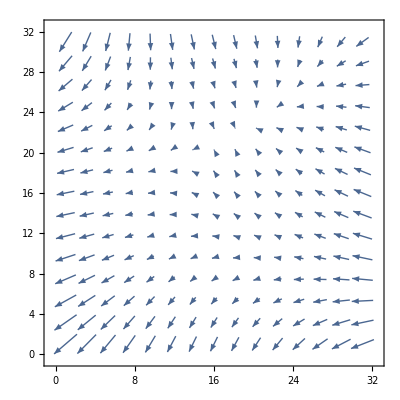

```mathematica
ListVectorPlot[data]
```

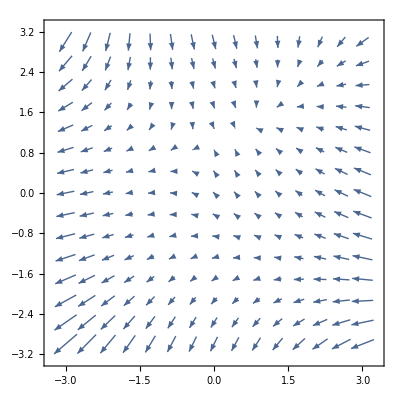

```mathematica
VectorPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
PieChart[{1,2,3,4,5}]
```

-Graphics-

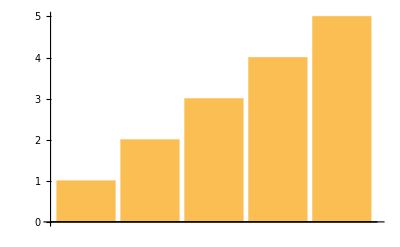

```mathematica
BarChart[{1,2,3,4,5}]
```

```mathematica
PieChart3D[{1,23,4,352,2,42}]
```

-Graphics3D-

```mathematica
BarChart3D[{1,124,2,2,2,1,1,2,42,4}]
```

-Graphics3D-

```mathematica
SectorChart[{{1,1},{1,2},{1,3}},SectorOrigin->{Automatic,1}]
```

-Graphics-